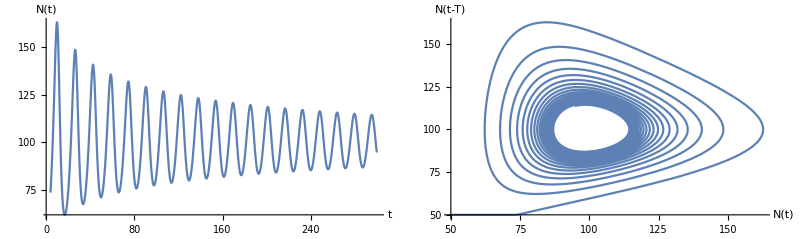

```mathematica
Clear["Global`*"]
a=20;
k=100;
r=0.1;
nzero=50;
T=3.9;
tmax= 300;
tmin=T;
(*{{tmin,tmax},{99.999, 100.003}}*)
GraphicsRow[{
Plot[Evaluate[n[t]/.First[NDSolve[{n'[t]==r*n[t]*(1-n[t-T]/k)*(n[t]/a-1),n[t/;t≤0]==nzero},n,{t,-T,tmax}]]],{t,tmin,tmax},PlotRange->All,ImageSize->{600,360},AxesLabel->{"t","N(t)"}],
ParametricPlot[Evaluate[{n[t],n[t-T]}/.First[NDSolve[{n'[t]==r*n[t]*(1-n[t-T]/k)*(n[t]/a-1),n[t/;t≤0]==nzero},n,{t,-T,tmax}]]],{t,0,tmax},PlotRange->All,ImageSize->{600,360},AxesLabel->{"N(t)","N(t-T)"}]},Spacings->2]
```

```mathematica
Solve[(λ1+i*λ2)*Exp[(λ1+i*λ2)*τ]==Exp[(λ1+i*λ2)(τ-d)](1-k/a), {λ1, λ2}]
Solve[(λ)*Exp[(λ)*τ]==Exp[(λ)(τ-d)](1-k/a), {λ}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^((λ1+i λ2) τ) (λ1+i λ2)==-4 ⅇ^((λ1+i λ2) (-d+τ)),{λ1,λ2}]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{λ→ProductLog[-4 d]/d}}